## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="FBA2";
fitLabel="";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "C:/massef";
kineticDataFileName =  "kinetic_data_manuscript.csv";

mainFolder = "fit_FBA2_test";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:C:\MASSef\examples\Manuscript\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00017 | 0.000167
0.000173 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00019 | 0.00016
0.00022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00024 | 0.00021
0.00027 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00085 | 0.0008075
0.0008925 |  | M | 7.5 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 10.5 | 9.83
11.2 | 1/s | 8 | 30 | trishcl | 0.05 | 
1 | fdp | Null | 8.17 | 7.73
8.6 | 1/s | 8 | 30 | trishcl | 0.05 | 
1 | fdp | Null | 10.33 | 10.03
10.63 | 1/s | 8 | 30 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | dhap | 0.00013 | 0.000119
0.000141 |  | Competitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.00003 | 0.000025
0.000035 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.00023 | 0.000188
0.000272 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kic | dhap | 9.×10^-6 | 7.8×10^-6
0.0000102 |  | Competitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.000118 | 0.000095
0.000141 |  | NonCompetitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.000221 | 0.000194
0.000248 |  | NonCompetitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,0,0,0};
s05Priorities = Null;
kcatPriorities = {1,0,0};
inhibitionPriorities={1,1,1,0,0,0};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00017 | 0.000167
0.000173 |  | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 10.5 | 9.83
11.2 | 1/s | 8 | 30 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | dhap | 0.00013 | 0.000119
0.000141 |  | Competitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.00003 | 0.000025
0.000035 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.00023 | 0.000188
0.000272 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
rxn
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

```mathematica
catalyticBranch={"E_FBA2[c] + fdp[c] <=> E_FBA2[c]&fdp",
				"E_FBA2[c]&fdp <=> E_FBA2[c]&dhap&g3p",
				"E_FBA2[c]&dhap&g3p <=> E_FBA2[c]&dhap + g3p[c]",
				"E_FBA2[c]&dhap <=> E_FBA2[c] + dhap[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((FBA2^c)_^+fdp^c⇌(FBA2^c&fdp^c)_^)^FBA21,((FBA2^c&dhap^c)_^⇌(FBA2^c)_^+dhap^c)^FBA22,((FBA2^c&fdp^c)_^⇌(FBA2^c&dhap^c&g3p^c)_^)^FBA23,((FBA2^c&dhap^c&g3p^c)_^⇌(FBA2^c&dhap^c)_^+g3p^c)^FBA24}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1=enzymeModelOrig["Reactions"];
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc=1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={{"prod_inhib_dhap",m["g3p","c"]->0},{"prod_inhib_g3p",m["dhap","c"]->0}};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

prod inhib

Generating flux equation...

{((FBA2^c&fdp^c)_^-((FBA2^c&dhap^c&g3p^c)_^)/K_FBA23) Volume_c k_FBA23^⟶}

Volume_c (-(FBA2^c&dhap^c&g3p^c)_^ k_FBA23^⟵+(FBA2^c&fdp^c)_^ k_FBA23^⟶)

Simplifying...

Added inhibition reactions:

{((FBA2^c)_^+dhap^c⇌(FBA2^c&dhap^c)_^)^FBA2_Kic_dhap_1_fdp,((FBA2^c)_^+g3p^c⇌(FBA2^c&g3p^c)_^)^FBA2_Kincc_g3p_1_fdp,((FBA2^c&g3p^c)_^+fdp^c⇌(FBA2^c&fdp^c&g3p^c)_^)^FBA2_NC_g3p,((FBA2^c&fdp^c)_^+g3p^c⇌(FBA2^c&fdp^c&g3p^c)_^)^FBA2_Kincu_g3p_1_fdp}

Generating flux equation...

{((FBA2^c&fdp^c)_^-((FBA2^c&dhap^c&g3p^c)_^)/K_FBA23) Volume_c k_FBA23^⟶}

Volume_c (-(FBA2^c&dhap^c&g3p^c)_^ k_FBA23^⟵+(FBA2^c&fdp^c)_^ k_FBA23^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating other relative rate forward equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	fdp[c]	g3p[c]	param_FBA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\haldaneRatio_1.txt"	0.00016
1	0	0.000017000000000000007	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\relRateFor_fdp.txt"	0.09090909090909094
1	0	0.00002694318427183895	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\relRateFor_fdp.txt"	0.1368068886032101
1	0	0.000042702069335662915	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\relRateFor_fdp.txt"	0.20076000891310194
1	0	0.0000676782189940945	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\relRateFor_fdp.txt"	0.28474724895080133
1	0	0.00010726274856163285	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\relRateFor_fdp.txt"	0.386863179846857
1	0	0.00017000000000000007	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\relRateFor_fdp.txt"	0.5000000000000001
1	0	0.0002694318427183895	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\relRateFor_fdp.txt"	0.6131368201531432
1	0	0.0004270206933566291	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\relRateFor_fdp.txt"	0.7152527510491988
1	0	0.0006767821899409458	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\relRateFor_fdp.txt"	0.7992399910868985
1	0	0.0010726274856163284	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\relRateFor_fdp.txt"	0.86319311139679
1	0	0.0017000000000000008	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\relRateFor_fdp.txt"	0.9090909090909091
1	0	1	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\absRateFor.txt"	10.5
1	0	1	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\absRateFor.txt"	10.5
1	0	1	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\absRateFor.txt"	10.5
1	0	1	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\absRateFor.txt"	10.5
1	0	1	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\absRateFor.txt"	10.5
1	0	1	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\absRateFor.txt"	10.5
1	0	1	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\absRateFor.txt"	10.5
1	0	1	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\absRateFor.txt"	10.5
1	0	1	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\absRateFor.txt"	10.5
1	0	1	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\absRateFor.txt"	10.5
1	0	1	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\absRateFor.txt"	10.5
1	0.000065	0.000017000000000000007	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.06250000000000003
1	0.000065	0.00005375872022286247	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.17411239489546837
1	0.000065	0.00017000000000000007	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.4000000000000001
1	0.000065	0.0005375872022286248	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6782688399674106
1	0.000065	0.0017000000000000008	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8695652173913043
1	0.00013	0.000017000000000000007	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.04761904761904764
1	0.00013	0.00005375872022286247	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.13652705949581437
1	0.00013	0.00017000000000000007	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.3333333333333335
1	0.00013	0.0005375872022286248	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6125741132772069
1	0.00013	0.0017000000000000008	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8333333333333333
1	0.00026	0.000017000000000000007	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.032258064516129045
1	0.00026	0.00005375872022286247	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.09535767393826002
1	0.00026	0.00017000000000000007	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.2500000000000001
1	0.00026	0.0005375872022286248	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.5131670194948621
1	0.00026	0.0017000000000000008	0	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.7692307692307693
1	0	0.000017000000000000007	0.00006500000000000001	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030349681108423142
1	0	0.00005375872022286247	0.00006500000000000001	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08852308825306443
1	0	0.00017000000000000007	0.00006500000000000001	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.22475570032573297
1	0	0.0005375872022286248	0.00006500000000000001	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.43782901894103
1	0	0.0017000000000000008	0.00006500000000000001	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.6252831898504759
1	0	0.000017000000000000007	0.00013000000000000002	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.01821541710665259
1	0	0.00005375872022286247	0.00013000000000000002	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.05425730412803112
1	0	0.00017000000000000007	0.00013000000000000002	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.14495798319327732
1	0	0.0005375872022286248	0.00013000000000000002	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.3075252527148365
1	0	0.0017000000000000008	0.00013000000000000002	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.4765193370165746
1	0	0.000017000000000000007	0.00026000000000000003	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.010121754437435824
1	0	0.00005375872022286247	0.00026000000000000003	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030581863846891433
1	0	0.00017000000000000007	0.00026000000000000003	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08476658476658477
1	0	0.0005375872022286248	0.00026000000000000003	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.1927783983056278
1	0	0.0017000000000000008	0.00026000000000000003	1	8	30	"C:\MASSef\examples\Manuscript\fit_FBA2_test\input\otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.32288254562470753

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	dhap[c]	fdp[c]	g3p[c]	param_FBA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.00015593331597644444
1	0	0.00001652183105507079	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.0909090909090909
1	0	0.000026185337566174318	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.13680688860321005
1	0	0.000041500963250925955	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.20076000891310186
1	0	0.00006577459413697128	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.2847472489508013
1	0	0.0001042457064845785	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.38686317984685686
1	0	0.0001652183105507079	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.49999999999999994
1	0	0.0002618533756617432	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.6131368201531431
1	0	0.0004150096325092596	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.7152527510491987
1	0	0.0006577459413697135	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.7992399910868982
1	0	0.0010424570648457849	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.8631931113967899
1	0	0.0016521831055070788	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.9090909090909092
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	12.334443212112031
1	0.000058979892851289964	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.06250000000000003
1	0.000058979892851289964	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.17411239489546837
1	0.000058979892851289964	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.4000000000000001
1	0.000058979892851289964	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6782688399674106
1	0.000058979892851289964	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8695652173913043
1	0.00011795978570257993	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.04761904761904764
1	0.00011795978570257993	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.13652705949581437
1	0.00011795978570257993	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.3333333333333335
1	0.00011795978570257993	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6125741132772069
1	0.00011795978570257993	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8333333333333333
1	0.00023591957140515986	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.032258064516129045
1	0.00023591957140515986	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.09535767393826002
1	0.00023591957140515986	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.2500000000000001
1	0.00023591957140515986	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.5131670194948621
1	0.00023591957140515986	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.7692307692307693
1	0	0.000017000000000000007	0.00006550559694017431	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030538502326548228
1	0	0.00005375872022286247	0.00006550559694017431	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08902893154671433
1	0	0.00017000000000000007	0.00006550559694017431	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.22577346360645933
1	0	0.0005375872022286248	0.00006550559694017431	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.4390019818156094
1	0	0.0017000000000000008	0.00006550559694017431	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.6259445813586448
1	0	0.000017000000000000007	0.00013101119388034862	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.018351621933368745
1	0	0.00005375872022286247	0.00013101119388034862	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.05463785271065735
1	0	0.00017000000000000007	0.00013101119388034862	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.14580581586504698
1	0	0.0005375872022286248	0.00013101119388034862	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.30868386452535285
1	0	0.0017000000000000008	0.00013101119388034862	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.47728800186120685
1	0	0.000017000000000000007	0.00026202238776069724	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.010205936112226723
1	0	0.00005375872022286247	0.00026202238776069724	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030823877288442242
1	0	0.00017000000000000007	0.00026202238776069724	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08534699636986248
1	0	0.0005375872022286248	0.00026202238776069724	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.19368986013823766
1	0	0.0017000000000000008	0.00026202238776069724	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.3235887720780135

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel,haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating inhibition data...

```mathematica
FilePrint[dataPathList[[8]]]
```

Priority	dhap[c]	fdp[c]	g3p[c]	param_FBA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/haldaneRatio_1.txt"	0.1
1	0	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.09090909090909094
1	0	0.00002694318427183895	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.1368068886032101
1	0	0.000042702069335662915	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.20076000891310194
1	0	0.0000676782189940945	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.28474724895080133
1	0	0.00010726274856163285	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.386863179846857
1	0	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.0002694318427183895	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.0004270206933566291	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.7152527510491988
1	0	0.0006767821899409458	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.7992399910868985
1	0	0.0010726274856163284	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/relRateFor_fdp.txt"	0.9090909090909091
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0	1	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/absRateFor.txt"	10.5
1	0.000065	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.06250000000000003
1	0.000065	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.17411239489546837
1	0.000065	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.4000000000000001
1	0.000065	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6782688399674106
1	0.000065	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8695652173913043
1	0.00013	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.04761904761904764
1	0.00013	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.13652705949581437
1	0.00013	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.3333333333333335
1	0.00013	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.6125741132772069
1	0.00013	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.8333333333333333
1	0.00026	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.032258064516129045
1	0.00026	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.09535767393826002
1	0.00026	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.2500000000000001
1	0.00026	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.5131670194948621
1	0.00026	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_dhap.txt"	0.7692307692307693
1	0	0.000017000000000000007	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030349681108423142
1	0	0.00005375872022286247	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08852308825306443
1	0	0.00017000000000000007	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.22475570032573297
1	0	0.0005375872022286248	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.43782901894103
1	0	0.0017000000000000008	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.6252831898504759
1	0	0.000017000000000000007	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.01821541710665259
1	0	0.00005375872022286247	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.05425730412803112
1	0	0.00017000000000000007	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.14495798319327732
1	0	0.0005375872022286248	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.3075252527148365
1	0	0.0017000000000000008	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.4765193370165746
1	0	0.000017000000000000007	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.010121754437435824
1	0	0.00005375872022286247	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.030581863846891433
1	0	0.00017000000000000007	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.08476658476658477
1	0	0.0005375872022286248	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.1927783983056278
1	0	0.0017000000000000008	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/MASSef/examples/FBA2/fit_FBA2_test/input/otherRateRelFor_fdp_prod_inhib_g3p.txt"	0.32288254562470753

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
numCPUs=2;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel, numCPUs];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel, numCPUs];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

python "C:\massef\python_code\src\run_fit_rel.py" "C:\MASSef\examples\Manuscript\fit_FBA2_test\input\psoParameters__20237122027.txt" "C:\MASSef\examples\Manuscript\fit_FBA2_test\input\lmaParameters__20237122027.txt" "C:\MASSef\examples\Manuscript\fit_FBA2_test\output\raw\summary__20237122027.txt" "C:\MASSef\examples\Manuscript\fit_FBA2_test\output\raw\psoResults__20237122027.txt" "C:\MASSef\examples\Manuscript\fit_FBA2_test\output\raw\lmaResults__20237122027.txt" 5 "C:\MASSef\examples\Manuscript\fit_FBA2_test\input\FBA2_.dat"

best_fit: 1.0767472692633644
best_fit: 0.615934159373409
best_fit: 1.042511382648869
best_fit: 3.086321194465389
best_fit: 2.615577614556818

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
(*datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];*)
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.0233856 | 0.000546886 | 8.38772×10^-6 | 5.24232 | 0.00016 | 0.000151612
1 | haldaneRatio_1 | 0.0233856 | 0.000546886 | 8.38772×10^-6 | 5.24232 | 0.00016 | 0.000151612
1 | haldaneRatio_1 | 0.0233856 | 0.000546886 | 8.38772×10^-6 | 5.24232 | 0.00016 | 0.000151612
1 | haldaneRatio_1 | 0.0233856 | 0.000546886 | 8.38772×10^-6 | 5.24232 | 0.00016 | 0.000151612
1 | haldaneRatio_1 | 0.0233856 | 0.000546886 | 8.38772×10^-6 | 5.24232 | 0.00016 | 0.000151612
1 | haldaneRatio_1 | 0.0233856 | 0.000546886 | 8.38772×10^-6 | 5.24232 | 0.00016 | 0.000151612
1 | haldaneRatio_1 | 0.0233856 | 0.000546886 | 8.38772×10^-6 | 5.24232 | 0.00016 | 0.000151612
1 | haldaneRatio_1 | 0.0233856 | 0.000546886 | 8.38772×10^-6 | 5.24232 | 0.00016 | 0.000151612
1 | haldaneRatio_1 | 0.0233856 | 0.000546886 | 8.38772×10^-6 | 5.24232 | 0.00016 | 0.000151612
1 | haldaneRatio_1 | 0.0233856 | 0.000546886 | 8.38772×10^-6 | 5.24232 | 0.00016 | 0.000151612
1 | haldaneRatio_1 | 0.0233856 | 0.000546886 | 8.38772×10^-6 | 5.24232 | 0.00016 | 0.000151612
1 | relRateFor_fdp | 0.0370862 | 0.00137539 | 0.00744088 | 8.18497 | 0.0909091 | 0.0834682
1 | relRateFor_fdp | 0.035284 | 0.00124496 | 0.0106753 | 7.80318 | 0.136807 | 0.126132
1 | relRateFor_fdp | 0.0327604 | 0.00107324 | 0.014587 | 7.26587 | 0.20076 | 0.186173
1 | relRateFor_fdp | 0.0294238 | 0.000865758 | 0.0186528 | 6.55066 | 0.284747 | 0.266094
1 | relRateFor_fdp | 0.0253321 | 0.000641714 | 0.0219199 | 5.66607 | 0.386863 | 0.364943
1 | relRateFor_fdp | 0.0207533 | 0.0004307 | 0.0233312 | 4.66625 | 0.5 | 0.476669
1 | relRateFor_fdp | 0.0161258 | 0.00026004 | 0.0223489 | 3.64501 | 0.613137 | 0.590788
1 | relRateFor_fdp | 0.0119062 | 0.000141758 | 0.0193424 | 2.70427 | 0.715253 | 0.69591
1 | relRateFor_fdp | 0.00840481 | 0.0000706408 | 0.0153188 | 1.91667 | 0.79924 | 0.783921
1 | relRateFor_fdp | 0.00571954 | 0.0000327131 | 0.0112935 | 1.30834 | 0.863193 | 0.8519
1 | relRateFor_fdp | 0.00378209 | 0.0000143042 | 0.00788253 | 0.867078 | 0.909091 | 0.901208
1 | absRateFor | 0.0067689 | 0.000045818 | 0.162384 | 1.54651 | 10.5 | 10.3376
1 | absRateFor | 0.0067689 | 0.000045818 | 0.162384 | 1.54651 | 10.5 | 10.3376
1 | absRateFor | 0.0067689 | 0.000045818 | 0.162384 | 1.54651 | 10.5 | 10.3376
1 | absRateFor | 0.0067689 | 0.000045818 | 0.162384 | 1.54651 | 10.5 | 10.3376
1 | absRateFor | 0.0067689 | 0.000045818 | 0.162384 | 1.54651 | 10.5 | 10.3376
1 | absRateFor | 0.0067689 | 0.000045818 | 0.162384 | 1.54651 | 10.5 | 10.3376
1 | absRateFor | 0.0067689 | 0.000045818 | 0.162384 | 1.54651 | 10.5 | 10.3376
1 | absRateFor | 0.0067689 | 0.000045818 | 0.162384 | 1.54651 | 10.5 | 10.3376
1 | absRateFor | 0.0067689 | 0.000045818 | 0.162384 | 1.54651 | 10.5 | 10.3376
1 | absRateFor | 0.0067689 | 0.000045818 | 0.162384 | 1.54651 | 10.5 | 10.3376
1 | absRateFor | 0.0067689 | 0.000045818 | 0.162384 | 1.54651 | 10.5 | 10.3376
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0316445 | 0.00100137 | 0.00439205 | 7.02728 | 0.0625 | 0.0581079
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0279867 | 0.000783258 | 0.0108662 | 6.24094 | 0.174112 | 0.163246
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0204884 | 0.000419774 | 0.0184323 | 4.60808 | 0.4 | 0.381568
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0110696 | 0.000122537 | 0.0170698 | 2.51667 | 0.678269 | 0.661199
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.00447416 | 0.0000200181 | 0.00891239 | 1.02492 | 0.869565 | 0.860653
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0287666 | 0.000827517 | 0.00305197 | 6.40915 | 0.047619 | 0.0445671
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0261532 | 0.000683991 | 0.007979 | 5.84426 | 0.136527 | 0.128548
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0203117 | 0.000412565 | 0.0152309 | 4.56926 | 0.333333 | 0.318102
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0118862 | 0.000141282 | 0.0165382 | 2.69978 | 0.612574 | 0.596036
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.00510759 | 0.0000260874 | 0.00974314 | 1.16918 | 0.833333 | 0.82359
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0257757 | 0.000664389 | 0.00185884 | 5.76239 | 0.0322581 | 0.0303992
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0241359 | 0.000582542 | 0.00515493 | 5.40589 | 0.0953577 | 0.0902027
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0200907 | 0.000403637 | 0.0113017 | 4.52069 | 0.25 | 0.238698
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.0131188 | 0.000172104 | 0.0152696 | 2.97556 | 0.513167 | 0.497897
1 | otherRateRelFor_fdp_prod_inhib_dhap | 0.00622601 | 0.0000387631 | 0.010949 | 1.42336 | 0.769231 | 0.758282
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.098977 | 0.00979645 | 0.00776841 | 25.5963 | 0.0303497 | 0.0381181
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.0700479 | 0.0049067 | 0.0154939 | 17.5027 | 0.0885231 | 0.104017
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.00900581 | 0.0000811045 | 0.00470934 | 2.09531 | 0.224756 | 0.229465
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.0720111 | 0.0051856 | 0.0668977 | 15.2794 | 0.437829 | 0.370931
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.132603 | 0.0175836 | 0.164524 | 26.312 | 0.625283 | 0.460759
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.0972693 | 0.00946132 | 0.0045727 | 25.1035 | 0.0182154 | 0.0227881
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.0658457 | 0.00433565 | 0.00888259 | 16.3712 | 0.0542573 | 0.0631399
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.0044339 | 0.0000196594 | 0.00147241 | 1.01575 | 0.144958 | 0.143486
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.107483 | 0.0115525 | 0.067422 | 21.924 | 0.307525 | 0.240103
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.193693 | 0.0375168 | 0.171457 | 35.9812 | 0.476519 | 0.305062
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.0374199 | 0.00140025 | 0.000910791 | 8.99835 | 0.0101218 | 0.0110325
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.0102353 | 0.000104761 | 0.000729301 | 2.38475 | 0.0305819 | 0.0313112
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.0544807 | 0.00296814 | 0.00999372 | 11.7897 | 0.0847666 | 0.0747729
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.160322 | 0.0257031 | 0.0595071 | 30.8682 | 0.192778 | 0.133271
1 | otherRateRelFor_fdp_prod_inhib_g3p | 0.260872 | 0.0680543 | 0.145801 | 45.1562 | 0.322883 | 0.177081

### Simulated Data and Best Fit Data Plot

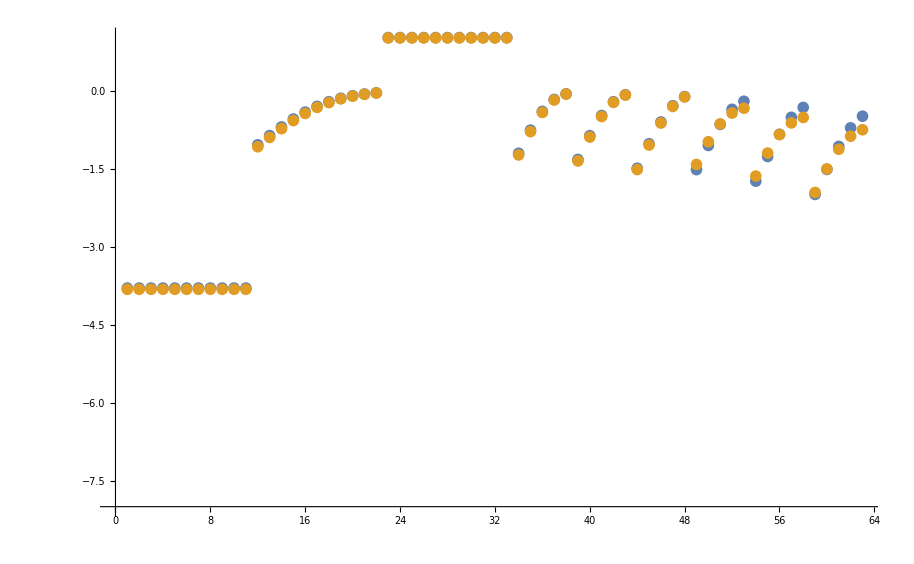

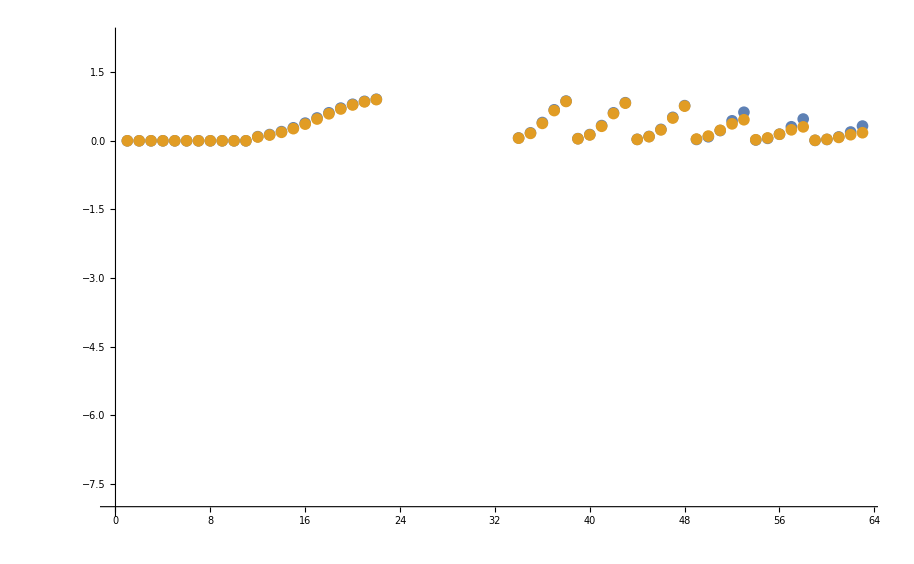

```mathematica
datasetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

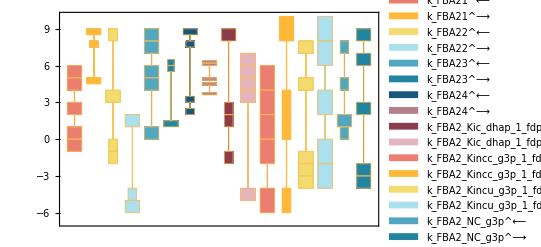

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

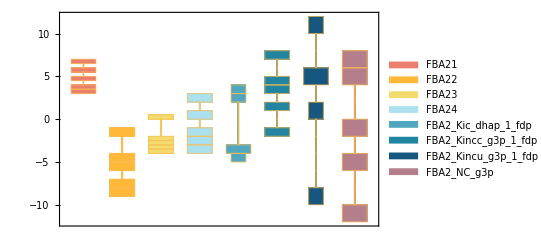

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

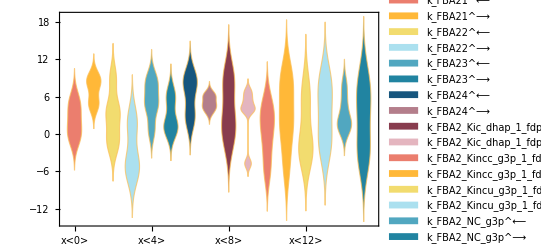

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

RegularExpression::msg22: Unmatched parentheses in RegularExpression[C:\MASSef\examples\Manuscript\fit_FBA2_test\input\(.*)\.txt]→$1.

General::stop: Further output of RegularExpression::msg22 will be suppressed during this calculation.

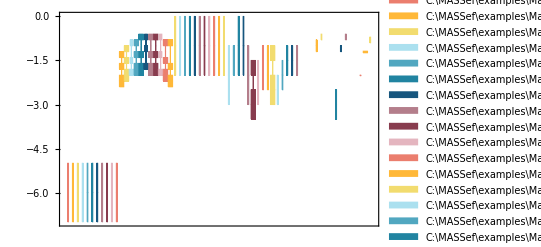

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.00017 | 0.000186639 | 9.78746

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
10.5 | 10.15 | 3.33299

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.00016 | 0.000151612 | 5.24232

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.00016 | 0.00016 | 1.75439×10^-7

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

Part::take: Cannot take positions 1 through 5 in {}.

MapThread::mptd: Object {}⟦1;;5⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}],MASSef`Private`x$43345,MASSef`Private`x$43345][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

Part::take: Cannot take positions 6 through 10 in {}.

General::stop: Further output of Part::take will be suppressed during this calculation.

MapThread::mptd: Object {}⟦6;;10⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}],MASSef`Private`x$43345,MASSef`Private`x$43345][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

MapThread::mptd: Object {}⟦11;;15⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}],MASSef`Private`x$43345,MASSef`Private`x$43345][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

data value | predicted value | error in %
0.00013 | Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$43345,MASSef`Private`x$43345],1,1][0]] | 769231. Abs[0.00013-Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$43345,MASSef`Private`x$43345],1,1][0]]]
0.00003 | Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$43345,MASSef`Private`x$43345],1,1][0]] | 3.33333×10^6 Abs[0.00003-Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{All,All,All}}],MASSef`Private`x$43345,MASSef`Private`x$43345],1,1][0]]]

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

Part::take: Cannot take positions 1 through 5 in {}.

MapThread::mptd: Object {}⟦1;;5⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}],MASSef`Private`x$47065,MASSef`Private`x$47065][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

Part::take: Cannot take positions 6 through 10 in {}.

General::stop: Further output of Part::take will be suppressed during this calculation.

MapThread::mptd: Object {}⟦6;;10⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}],MASSef`Private`x$47065,MASSef`Private`x$47065][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

MapThread::mptd: Object {}⟦11;;15⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}],MASSef`Private`x$47065,MASSef`Private`x$47065][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{LinearModelFit[MapThread[{Times[«2»],Times[«2»]}&,{{}⟦Span[«2»]⟧,{}⟦Span[«2»]⟧}],MASSef`Private`x$47065,MASSef`Private`x$47065][ParameterTableEntries],LinearModelFit[MapThread[{Times[«2»],Times[«2»]}&,{{}⟦Span[«2»]⟧,{}⟦Span[«2»]⟧}],MASSef`Private`x$47065,MASSef`Private`x$47065][ParameterTableEntries],LinearModelFit[MapThread[{Times[«2»],Times[«2»]}&,{{}⟦Span[«2»]⟧,{}⟦Span[«2»]⟧}],MASSef`Private`x$47065,MASSef`Private`x$47065][ParameterTableEntries]}}]; dimensions are 0 and 3.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

data value | predicted value | error in %
0.00023 | Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{LinearModelFit[MapThread[{1/#1,1/#2}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}],MASSef`Private`x$47065,MASSef`Private`x$47065][ParameterTableEntries],LinearModelFit[MapThread[{1/#1,1/#2}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}],MASSef`Private`x$47065,MASSef`Private`x$47065][ParameterTableEntries],LinearModelFit[MapThread[{1/#1,1/#2}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}],MASSef`Private`x$47065,MASSef`Private`x$47065][ParameterTableEntries]}}],MASSef`Private`x$47065,MASSef`Private`x$47065],1,1][0]] | 434783. Abs[0.00023-Abs[InverseFunction[LinearModelFit[MapThread[{#1,#2}&,{{},{LinearModelFit[MapThread[{1/#1,1/#2}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}],MASSef`Private`x$47065,MASSef`Private`x$47065][ParameterTableEntries],LinearModelFit[MapThread[{1/#1,1/#2}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}],MASSef`Private`x$47065,MASSef`Private`x$47065][ParameterTableEntries],LinearModelFit[MapThread[{1/#1,1/#2}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}],MASSef`Private`x$47065,MASSef`Private`x$47065][ParameterTableEntries]}}],MASSef`Private`x$47065,MASSef`Private`x$47065],1,1][0]]]

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::take: Cannot take positions 1 through 5 in {}.

MapThread::mptd: Object {}⟦1;;5⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦1;;5⟧,{}⟦1;;5⟧}],MASSef`Private`x$48492,MASSef`Private`x$48492][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

Part::take: Cannot take positions 6 through 10 in {}.

General::stop: Further output of Part::take will be suppressed during this calculation.

MapThread::mptd: Object {}⟦6;;10⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}] has only 0 of required 1 dimensions.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦6;;10⟧,{}⟦6;;10⟧}],MASSef`Private`x$48492,MASSef`Private`x$48492][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

MapThread::mptd: Object {}⟦11;;15⟧ at position {2, 1} in MapThread[{1/#1,1/#2}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Part::partd: Part specification LinearModelFit[MapThread[{1/Slot[«1»],1/Slot[«1»]}&,{{}⟦11;;15⟧,{}⟦11;;15⟧}],MASSef`Private`x$48492,MASSef`Private`x$48492][ParameterTableEntries]⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{All,All,All}}]; dimensions are 0 and 3.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[{#1,#2}&,{{},{LinearModelFit[MapThread[{Times[«2»],Times[«2»]}&,{{}⟦Span[«2»]⟧,{}⟦Span[«2»]⟧}],MASSef`Private`x$49745,MASSef`Private`x$49745][ParameterTableEntries],LinearModelFit[MapThread[{Times[«2»],Times[«2»]}&,{{}⟦Span[«2»]⟧,{}⟦Span[«2»]⟧}],MASSef`Private`x$49745,MASSef`Private`x$49745][ParameterTableEntries],LinearModelFit[MapThread[{Times[«2»],Times[«2»]}&,{{}⟦Span[«2»]⟧,{}⟦Span[«2»]⟧}],MASSef`Private`x$49745,MASSef`Private`x$49745][ParameterTableEntries]}}]; dimensions are 0 and 3.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

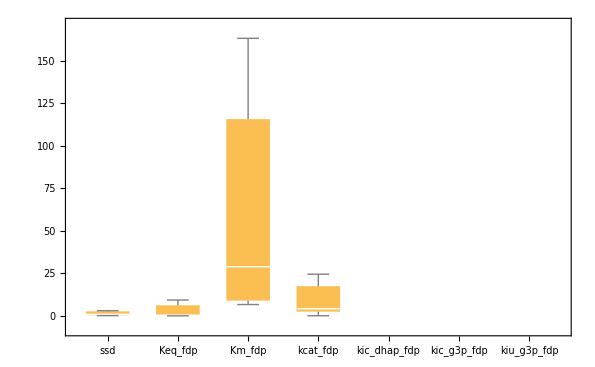

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```